This notebook contains the functions used for manipulating and minimizing the Randlett bird, and creating Figure 4 in the paper “Robust folding of elastic origami”. This notebook requires the mechanisms.m package, located at [ https://github.com/cdsantan/mechanisms ]. If there are version incompatibilities, please email marvlee@umass.edu or cdsantan@syr.edu for an older version.

```mathematica
$HistoryLength=0;
SetDirectory[NotebookDirectory[]]
```

/Users/mel/Downloads

```mathematica
<<"mechanisms`"
```

```mathematica
$mechanismsVersion
```

0.85

## Creating and initializing the Randlett bird

This initial setup creates the Randlett bird and sets it up so that the length dependencies on individual torsion springs are built-in, so the origami can be given K_face and K_fold values as described in the paper.

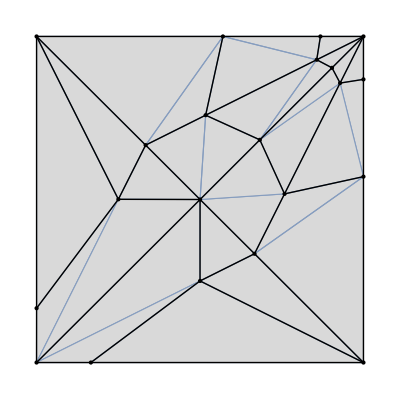

```mathematica
m=origami["RandlettBird"];

(*the shortest fold's length*)
l=Min[displacementLength[m,listCells[m,"active"]]];

rb =
(*set active fold stiffnesses*) 
changeCellData[ fold,listCells[m,"passive"], "torsionalStiffness"->(kface*displacementLength[m,listCells[m,"passive"]])]@
(*set passive fold stiffnesses*)
changeCellData[ fold,listCells[m,"active"], "torsionalStiffness"->(kfold*displacementLength[m,listCells[m,"active"]])]@
(*length stiffnesses according to face areas*)
changeCellData[rigidBar,listEdges[m],"stiffness" -> Map[Mean[Norm/@normalVector[ m , #,"normalize"->False]]/3& , connectivity[m,"edges"->"faces"]]]@m
```

Now compile the mechanism energy.

```mathematica
ce=compiledMechanismEnergy[rb]
```

compiledMechanismEnergy[{kfold, kface}]

## Functions

### birdsQ[]

Checks if an object is a folded Randlett bird with the desired associations (defined later).

```mathematica
birdsQ[ birds_Association ] := And @@ (KeyExistsQ[ birds, # ]& /@ {"method","reference","moduli","seed","norms","energies","birds"})
birdsQ[ _ ] := False
```

### gradentMagnitude[]

Checks the magnitude of the energy gradient as a set of vertex positions. Used to check validity of critical points.

```mathematica
gradientMagnitude::usage="gradientMagnitude[ compiledEnergy, {data1 -> value1, ...} ][ pos ] takes a single or several vertex positions and computes the norm of the gradient.";

gradientMagnitude[ ce_?compiledMechanismEnergyQ, data : {__Rule} ][pos_?vertexCoordinatesQ] :=
	Norm[ce["gradient"][Flatten[pos],ce["data"]/.data]]

gradientMagnitude[ ce_?compiledMechanismEnergyQ, data : {__Rule} ][pos : {__?vertexCoordinatesQ}] :=
With[{ flatPos = Flatten /@ pos, d = ce["data"]/.data },
	Norm /@ (ce["gradient"][#,d]& /@ flatPos)
]
```

### averageDistanceBetweenVertices[]

Calculates the average distance between corresponding vertices of two mechanisms. Used to determine which fold patterns are the same in groupBirds[].

```mathematica
averageDistanceBetweenVertices::usage="averageDistanceBetweenVertices[ pos1, pos2 ] computes the mean distance between corresponding vertices";

averageDistanceBetweenVertices[ pos1_?MatrixQ, pos2_?MatrixQ ] := Mean[Norm/@(pos1-pos2)] /; Dimensions[pos1]==Dimensions[pos2]
```

### minimizeBirds[]

See usage.

```mathematica
minimizeBirds::usage=
"minimizeBirds[ m, compiled energy, {kface -> value1, kfold -> value2}, {r, N}, (options) ] starts with N flat birds whose vertices  have been randomly displaced by a distribution of width r.
minimizeBirds[ m, compiled energy, bird data, (options) ] reminimizes the results from a previous minimization where bird data is the output of minimizeBirds[].

options is specifically the Method option of FindMinimum. The default is \"QuasiNewton\".";
```

```mathematica
minimizeBirds[m_?mechanismQ, ce_?compiledMechanismEnergyQ, moduli : {__Rule}, {randomness_?NumericQ, number_Integer}, methodOptions_ : "QuasiNewton"] :=
With[{initialBirds = randomDisplacements[m,number,
		"distribution" -> NormalDistribution[0,randomness*Min[displacementLength[m,listEdges[m]]]]
	]},
	minimizeBirds[m, ce, 
		Association[
			"moduli" -> moduli,
			"randomness" -> randomness,
			"seed" -> initialBirds
		],
		methodOptions
	]
]

minimizeBirds[ m_?mechanismQ, ce_?compiledMechanismEnergyQ, birds_Association, methodOptions_ : "QuasiNewton" ] :=
Module[ { reference , refEnergy , initial, energies, minimizedBirds, time},

	Print[birds["moduli"]];

	(*If needed, compute a reference bird*)
	If[ Not @ KeyExistsQ[ birds, "reference" ],
		{refEnergy, reference} = minimizeEnergy[ m, ce /. birds[ "moduli" ], 
			"initial" -> origamiData["RandlettBird"]["folded coordinates"], (* <---- insert your folded coordinates here*)
			MaxIterations->10^6,
			Method -> methodOptions
		];
		Print["reference bird results: ", refEnergy, "->", gradientMagnitude[ ce , birds["moduli"] ][ reference ]],

		reference = birds["reference"]
	];
	
	initial = If[ Not@KeyExistsQ[ birds, "birds" ], birds["seed"], birds["birds"]];

	{time, {energies, minimizedBirds}} = Timing[ Transpose @ minimizeEnergy[m , ce /. birds["moduli"],
			"initial" -> initial,
			MaxIterations->10^6,
			Method -> methodOptions
	]];

	Print["  time=", time,
		",  norm range = ", ({Min[#],Max[#]}&) @ gradientMagnitude[ ce , birds["moduli"] ][ minimizedBirds ],
		", # of error free birds = ", Length@Select[energies ,RealQ ]
	];
	
	Association[
		"method" -> If[KeyExistsQ[ birds, "method" ], { birds["method"], Flatten@{methodOptions} } , Flatten@{methodOptions} ],
		"randomness" -> If[ KeyExistsQ[ birds, "randomness" ], birds["randomness"], 0 ],
		"moduli" -> birds["moduli"],
		"reference" -> If[ KeyExistsQ[ birds, "reference"], birds["reference"], reference ],
		"seed" -> birds["seed"],
		"norms" -> gradientMagnitude[ ce , birds["moduli"] ][ minimizedBirds ],
		"energies" -> energies,
		"birds" -> (alignMechanism[ reference , # ]& /@ minimizedBirds)
	]
	
] /; KeyExistsQ[ birds, "moduli" ] && KeyExistsQ[ birds, "seed" ]
```

### addBirds[], joinBirds[]

addBirds[] combines the data from two associations generated by minimzeBirds[], mostly used in joinBirds[] and increaseBirds[]. joinBirds[] combines two lists of birds according to their K_fold and K_face (moduli) values.

```mathematica
ClearAll[addBirds];

addBirds::usage="addBirds[ data1, data2 ] creates a larger data structure combining the data from two smaller ones.
This only does some basic checks to make sure you are combining compatible data.";

(*function to combine data from several runs with the same modulus into a larger data structure of the same type.*)
addBirds[ birds1_Association, birds2_Association ] :=
With[ {
r1 = If[KeyExistsQ[ birds1, "randomness" ], birds1["randomness"], -1 ], 
r2 = If[KeyExistsQ[ birds2, "randomness" ], birds2["randomness"], -1 ],
method = If[ First@Flatten[birds1["method"]] === First@Flatten[birds2["method"]], birds1["method"], birds1["method"] ] (*one could imagine something better*)
},
	Association[
		"method" -> method, (*these should be the same*)
		"randomness" -> Max[ r1,r2 ],
		"moduli" -> birds1["moduli"],
		"reference" -> birds1["reference"] (*these should be the same anyway up to numerical error*),
		"seed" -> Join[ birds1["seed"], birds2["seed"] ],
		"norms" -> Join[ birds1["norms"], birds2["norms"] ],
		"energies" -> Join[ birds1["energies"], birds2["energies"] ],
		"birds" -> Join[ birds1["birds"], (alignMechanism[ birds1["reference"], # ] & /@ birds2["birds"]) ]
	]
] /; sameModuliQ[ birds1, birds2 ] && methodsQ[ birds1, birds2]

methodsQ[ birds1_Association, birds2_Association ] := 
	If[ First@Flatten[birds1["method"]] =!= First@Flatten[birds2["method"]], 
		Message[addBirds::nometh]; True,
		True
	] /; KeyExistsQ[birds1 , "method" ] && KeyExistsQ[birds2 , "method" ]
methodsQ[ _, _ ] := (Message[addBirds::nometh]; False)

sameModuliQ[ birds1_Association, birds2_Association ] := With[ {out = And[
	Chop[(kface /. birds1["moduli"]) - (kface /. birds2["moduli"])]==0,
	Chop[(kfold /. birds1["moduli"]) - (kfold /. birds2["moduli"])]==0
]}, 
	If[ Not@out, Message[addBirds::nomatch]]; out
] /; KeyExistsQ[ birds1, "moduli"] && KeyExistsQ[ birds2, "moduli" ]
sameModuliQ[_,_ ]:= (Message[addBirds::notbirds]; False)

addBirds::random = "Two sets of data have different randomnesses.";
addBirds::diffmeth = "Methods are not the same.";
addBirds::nometh = "Both sets of data have different minimization methods. Just keeping the first.";
addBirds::notbirds = "Bird data isn't complete enough.";
addBirds::nomatch = "The two bird associations have different moduli and cannot be combined.";
```

```mathematica
joinBirds::usage="joinBirds[{birds1, birds2, ...}, {birds3, ...}}] combines two lists of birds according to their moduli into a single list.";

joinBirds[ list1 : {__Association}, list2 : {__Association} ]:=With[
{
	grouped = Gather[ Join[list1,list2], Chop[Norm[({kface,kfold}/.#1["moduli"]) - ({kface,kfold}/.#2["moduli"])]]==0& ]
},
	If[ Length[#]==2,
		addBirds @@ #,
		First@#
	]& /@ grouped
]
```

### increaseBirds[]

Adds initial minimizations according to input value if the total number of valid minimizations is below the target value. Used to get to the target values of at least 500 minimized birds or 10 times the number of distinct states observed.

```mathematica
increaseBirds::usage=
"increaseBirds[ m, compiled energy, birds, number to add, target number ] adds additional minimizations if the number of birds is below a target.";

increaseBirds[ m_?mechanismQ, ce_?compiledMechanismEnergyQ, birds_Association, number_Integer, target_Integer ] := 
Module[
{
	out,
	method = If[ Length@Dimensions[birds["method"]] ≤ 1, birds["method"], birds["method"][[1,1]] ]
},
	If[ Count[ birds["energies"], _?NumericQ ] < target, 
		addBirds[
			birds,
			minimizeBirds[m, ce, birds["moduli"], { birds["randomness"], number }, method ]
		],
		birds
	]
] /; KeyExistsQ[ birds, "randomness" ] && KeyExistsQ[ birds, "energies" ] && KeyExistsQ[ birds, "method" ]
```

### groupBirds[]

Sorts a set of folded Randlett birds into groups according to the average of the distance between corresponding vertices, with the threshold for acceptable distance supplied.

```mathematica
groupBirds[threshold_?NumericQ][ birds_?birdsQ ] := Gather[ birds["birds"], averageDistanceBetweenVertices[#1,#2]<threshold& ]
```

### filterByEnergy[]

Meant to be used as filterByEnergy[birds,NumericQ] in order to extract the minima from data generated using the above functions that did not throw any errors.

```mathematica
filterByEnergy::usage="filterByEnergy[ bird data, filter ] filters birds according to whether filter[ energy ] returns True or False. This is mostly meant to be used as filterByEnergy[ birds, NumericQ ] to extract the good minima.";

filterByEnergy[ data_?birdsQ , filterFunction_ ] :=
With[ { selectorList = filterFunction /@ data["energies"] }, 
	If[ And @@ (BooleanQ/@selectorList) , 
		Association[
			"method" -> data["method"],
			"reference" -> data["reference"],
			"moduli" -> data["moduli"],
			"seed" -> Pick[ data["seed"], selectorList ],
			"norms" -> Pick[ data["norms"], selectorList ],
			"energies" -> Pick[ data["energies"], selectorList ],
			"birds" -> Pick[ data["birds"], selectorList ]
		],
		
		$Failed
	]
]
```

## Sample Data Run

In this section is a sample of how data was generated. After a quick check of number of different fold patterns, this process with reiterated until the desired number of birds (at least 500 or 10 times the number of fold patterns) was reached. Full data sets are included on the GitHub.

```mathematica
Quiet[out=minimizeBirds[ rb, ce, {kface->10^(-7), kfold->10^#}, {0.5, 500} ,{"QuasiNewton","StepMemory"->Infinity,"StepControl"->{"LineSearch","MaxRelativeStepSize"->1}}]&/@Range[-8,-5,0.25]];
```

{kface→1/10000000,kfold→1.×10^-8}

reference bird results: 1.54817×10^-8->7.38188×10^-12

time=214.456,  norm range = {1.72584×10^-13,0.0000231199}, # of error free birds = 401

{kface→1/10000000,kfold→1.77828×10^-8}

reference bird results: 2.19073×10^-8->3.68566×10^-12

time=217.724,  norm range = {5.32497×10^-13,0.0000328395}, # of error free birds = 358

{kface→1/10000000,kfold→3.16228×10^-8}

reference bird results: 3.21784×10^-8->9.8955×10^-12

time=179.922,  norm range = {1.47293×10^-12,0.0000368071}, # of error free birds = 256

{kface→1/10000000,kfold→5.62341×10^-8}

reference bird results: 4.9174×10^-8->1.0181×10^-11

time=146.954,  norm range = {1.11976×10^-12,0.0000673424}, # of error free birds = 213

{kface→1/10000000,kfold→1.×10^-7}

reference bird results: 7.79068×10^-8->1.0303×10^-11

time=122.004,  norm range = {2.12226×10^-12,0.000147481}, # of error free birds = 190

{kface→1/10000000,kfold→1.77828×10^-7}

reference bird results: 1.27193×10^-7->1.27525×10^-11

time=86.1928,  norm range = {1.40022×10^-12,0.000291357}, # of error free birds = 96

{kface→1/10000000,kfold→3.16228×10^-7}

reference bird results: 2.12644×10^-7->7.59325×10^-12

time=58.7627,  norm range = {4.12375×10^-12,0.000354595}, # of error free birds = 53

{kface→1/10000000,kfold→5.62341×10^-7}

reference bird results: 3.62118×10^-7->1.36452×10^-11

time=45.8728,  norm range = {6.34106×10^-12,0.000433502}, # of error free birds = 28

{kface→1/10000000,kfold→1.×10^-6}

reference bird results: 6.25424×10^-7->3.83812×10^-11

time=39.184,  norm range = {1.99834×10^-11,0.000801435}, # of error free birds = 10

{kface→1/10000000,kfold→1.77828×10^-6}

reference bird results: 1.09124×10^-6->3.96426×10^-11

time=34.2321,  norm range = {2.18381×10^-11,0.00237275}, # of error free birds = 9

{kface→1/10000000,kfold→3.16228×10^-6}

reference bird results: 1.91665×10^-6->1.51673×10^-11

time=31.0785,  norm range = {4.34812×10^-11,0.00173524}, # of error free birds = 8

{kface→1/10000000,kfold→5.62341×10^-6}

reference bird results: 3.37873×10^-6->5.08607×10^-11

time=28.2234,  norm range = {2.64949×10^-11,0.00337066}, # of error free birds = 13

{kface→1/10000000,kfold→0.00001}

reference bird results: 5.96304×10^-6->2.77851×10^-10

time=26.2358,  norm range = {6.55655×10^-11,0.00458898}, # of error free birds = 19

Now use the increaseBirds[] function to increase the number of birds if there are fewer than 500:

```mathematica
Quiet[testout2=increaseBirds[ rb, ce, #, 400,500 ]&/@out;]
```

{kface→1/10000000,kfold→1.×10^-8}

reference bird results: 1.54817×10^-8->7.38188×10^-12

time=181.252,  norm range = {4.00285×10^-13,0.0000298861}, # of error free birds = 300

{kface→1/10000000,kfold→1.77828×10^-8}

reference bird results: 2.19073×10^-8->3.68566×10^-12

time=176.51,  norm range = {1.13882×10^-12,0.0000245362}, # of error free birds = 291

{kface→1/10000000,kfold→3.16228×10^-8}

reference bird results: 3.21784×10^-8->9.8955×10^-12

time=141.772,  norm range = {1.49318×10^-12,0.0000421362}, # of error free birds = 222

{kface→1/10000000,kfold→5.62341×10^-8}

reference bird results: 4.9174×10^-8->1.0181×10^-11

time=117.569,  norm range = {1.886×10^-12,0.0000566611}, # of error free birds = 173

{kface→1/10000000,kfold→1.×10^-7}

reference bird results: 7.79068×10^-8->1.0303×10^-11

time=98.0872,  norm range = {1.99543×10^-12,0.000109551}, # of error free birds = 147

{kface→1/10000000,kfold→1.77828×10^-7}

reference bird results: 1.27193×10^-7->1.27525×10^-11

time=70.9393,  norm range = {3.30096×10^-12,0.000160613}, # of error free birds = 91

{kface→1/10000000,kfold→3.16228×10^-7}

reference bird results: 2.12644×10^-7->7.59325×10^-12

time=49.7637,  norm range = {4.14134×10^-12,0.000710126}, # of error free birds = 48

{kface→1/10000000,kfold→5.62341×10^-7}

reference bird results: 3.62118×10^-7->1.36452×10^-11

time=37.7195,  norm range = {1.15335×10^-11,0.000508547}, # of error free birds = 18

{kface→1/10000000,kfold→1.×10^-6}

reference bird results: 6.25424×10^-7->3.83812×10^-11

time=31.7647,  norm range = {9.89158×10^-12,0.000831486}, # of error free birds = 8

{kface→1/10000000,kfold→1.77828×10^-6}

reference bird results: 1.09124×10^-6->3.96426×10^-11

time=27.5114,  norm range = {1.86734×10^-11,0.00144379}, # of error free birds = 5

{kface→1/10000000,kfold→3.16228×10^-6}

reference bird results: 1.91665×10^-6->1.51673×10^-11

time=24.7074,  norm range = {3.06388×10^-11,0.00290212}, # of error free birds = 6

{kface→1/10000000,kfold→5.62341×10^-6}

reference bird results: 3.37873×10^-6->5.08607×10^-11

time=22.0229,  norm range = {3.06781×10^-11,0.0038613}, # of error free birds = 4

{kface→1/10000000,kfold→0.00001}

reference bird results: 5.96304×10^-6->2.77851×10^-10

time=20.7173,  norm range = {6.0521×10^-11,0.00402331}, # of error free birds = 12

```mathematica
Count[#["energies"],_?NumericQ]&/@testout2
```

{701,649,478,386,337,187,101,46,18,14,14,17,31}

Continue adding birds.

```mathematica
Quiet[testout3=increaseBirds[ rb, ce, #, 400,500 ]&/@testout2;]
```

{kface→1/10000000,kfold→3.16228×10^-8}

reference bird results: 3.21784×10^-8->9.8955×10^-12

time=145.772,  norm range = {6.72217×10^-13,0.0000485575}, # of error free birds = 218

{kface→1/10000000,kfold→5.62341×10^-8}

reference bird results: 4.9174×10^-8->1.0181×10^-11

time=115.034,  norm range = {1.14938×10^-12,0.0000800044}, # of error free birds = 167

{kface→1/10000000,kfold→1.×10^-7}

reference bird results: 7.79068×10^-8->1.0303×10^-11

time=97.8371,  norm range = {1.36748×10^-12,0.0000974005}, # of error free birds = 137

{kface→1/10000000,kfold→1.77828×10^-7}

reference bird results: 1.27193×10^-7->1.27525×10^-11

time=67.2831,  norm range = {5.09226×10^-12,0.000141197}, # of error free birds = 73

{kface→1/10000000,kfold→3.16228×10^-7}

reference bird results: 2.12644×10^-7->7.59325×10^-12

time=47.5528,  norm range = {5.21725×10^-12,0.000297646}, # of error free birds = 48

{kface→1/10000000,kfold→5.62341×10^-7}

reference bird results: 3.62118×10^-7->1.36452×10^-11

time=36.6307,  norm range = {1.03383×10^-11,0.000389865}, # of error free birds = 25

{kface→1/10000000,kfold→1.×10^-6}

reference bird results: 6.25424×10^-7->3.83812×10^-11

time=30.5798,  norm range = {2.34201×10^-11,0.0005362}, # of error free birds = 5

{kface→1/10000000,kfold→1.77828×10^-6}

reference bird results: 1.09124×10^-6->3.96426×10^-11

time=27.1011,  norm range = {2.97934×10^-11,0.00120692}, # of error free birds = 7

{kface→1/10000000,kfold→3.16228×10^-6}

reference bird results: 1.91665×10^-6->1.51673×10^-11

time=23.9461,  norm range = {2.86735×10^-11,0.00160142}, # of error free birds = 8

{kface→1/10000000,kfold→5.62341×10^-6}

reference bird results: 3.37873×10^-6->5.08607×10^-11

time=21.6617,  norm range = {6.686×10^-11,0.00225014}, # of error free birds = 5

{kface→1/10000000,kfold→0.00001}

reference bird results: 5.96304×10^-6->2.77851×10^-10

time=20.0049,  norm range = {4.22956×10^-11,0.00258146}, # of error free birds = 13

```mathematica
Count[#["energies"],_?NumericQ]&/@testout3
```

{701,649,696,553,474,260,149,71,23,21,22,22,44}

Continue adding birds

```mathematica
Quiet[testout4=increaseBirds[ rb, ce, #, 400,500 ]&/@testout3;]
```

{kface→1/10000000,kfold→1.×10^-7}

reference bird results: 7.79068×10^-8->1.0303×10^-11

time=95.3199,  norm range = {1.55093×10^-12,0.000141817}, # of error free birds = 139

{kface→1/10000000,kfold→1.77828×10^-7}

reference bird results: 1.27193×10^-7->1.27525×10^-11

time=66.8273,  norm range = {3.90909×10^-12,0.000849279}, # of error free birds = 72

{kface→1/10000000,kfold→3.16228×10^-7}

reference bird results: 2.12644×10^-7->7.59325×10^-12

time=45.3257,  norm range = {5.24817×10^-12,0.000273081}, # of error free birds = 36

{kface→1/10000000,kfold→5.62341×10^-7}

reference bird results: 3.62118×10^-7->1.36452×10^-11

time=37.1455,  norm range = {7.58341×10^-12,0.000401443}, # of error free birds = 20

{kface→1/10000000,kfold→1.×10^-6}

reference bird results: 6.25424×10^-7->3.83812×10^-11

time=30.6784,  norm range = {1.12452×10^-11,0.00072243}, # of error free birds = 13

{kface→1/10000000,kfold→1.77828×10^-6}

reference bird results: 1.09124×10^-6->3.96426×10^-11

time=27.7533,  norm range = {1.08386×10^-11,0.00168926}, # of error free birds = 10

{kface→1/10000000,kfold→3.16228×10^-6}

reference bird results: 1.91665×10^-6->1.51673×10^-11

time=24.6365,  norm range = {2.84404×10^-11,0.0030542}, # of error free birds = 7

{kface→1/10000000,kfold→5.62341×10^-6}

reference bird results: 3.37873×10^-6->5.08607×10^-11

time=22.5425,  norm range = {4.4472×10^-11,0.00252113}, # of error free birds = 7

{kface→1/10000000,kfold→0.00001}

reference bird results: 5.96304×10^-6->2.77851×10^-10

time=20.3574,  norm range = {3.38051×10^-11,0.00273705}, # of error free birds = 8

```mathematica
Count[#["energies"],_?NumericQ]&/@testout4
```

{701,649,696,553,613,332,185,91,36,31,29,29,52}

This has not reached the cutoff point yet, and so would continue this pattern, but this is enough for the sake of demonstration.

## Data Analysis

Now a walk through of analyzing the data. This requires the “newrand...” files, which contain the data encoded in Fig. 4 saved as Mathematica objects. Start by loading the data in:

```mathematica
data4=<<"newrandfin10E-4";
data45=<<"newrandfin10E-45";
data5=<<"newrandfin10E-5";
data55=<<"newrandfin10E-55";
data6=<<"newrandfin10E-6";
data65=<<"newrandfin2-10E-65";
data7=<<"newrandfin3-10E-7";
datafold45=<<"newrandfinfold10E-45";
datafold425=<<"newrandfinfold10E-425";
```

Next, use  filterByEnergy[] to sort out the minima from the data sets that did not generate errors. This is the number of birds that we were counting above in the sample data run.

```mathematica
birds4= filterByEnergy[#,NumericQ]&/@data4;
birds45= filterByEnergy[#,NumericQ]&/@data45;
birds5= filterByEnergy[#,NumericQ]&/@data5;
birds55= filterByEnergy[#,NumericQ]&/@data55;
birds6= filterByEnergy[#,NumericQ]&/@data6;
birds65= filterByEnergy[#,NumericQ]&/@data65;
birds7= filterByEnergy[#,NumericQ]&/@data7;
birdsfold425=filterByEnergy[#,NumericQ]&/@datafold425;
birdsfold45=filterByEnergy[#,NumericQ]&/@datafold45;
```

To find the appropriate threshold to use for groupBirds[], plot the number of distinct configurations found by groupBirds[] at different threshold values. We will be looking for a plateau:

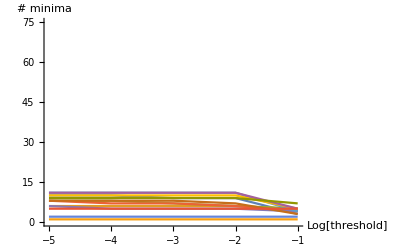

```mathematica
ListPlot[Table[{#,Length[groupBirds[10^#][birds5[[i]]]]}& /@ Range[-5,-1],{i,1,Length[birds5]}],Joined->True,AxesLabel->{"Log[threshold]","# minima"},PlotRange->{0,75}]
```

We ran this for every data set, the above is merely an example. A threshold of 10^(-3) is within the plateaus for all data sets, so we will use that:

```mathematica
threshold = 10^(-3);
```

Now we can group all of the data sets:

```mathematica
test4=groupBirds[ threshold]/@ birds4;
test45=groupBirds[ threshold]/@ birds45;
test5=groupBirds[ threshold]/@ birds5;
test55=groupBirds[ threshold]/@ birds55;
test6=groupBirds[ threshold]/@ birds6;
test65=groupBirds[ threshold]/@ birds65;
test7=groupBirds[ threshold]/@ birds7;
testfold425=groupBirds[ threshold]/@ birdsfold425;
testfold45=groupBirds[ threshold]/@ birdsfold45;
```

And count the number of distinct states:

```mathematica
statedata4=Table[{Log[10,kfold]/.data4[[i]]["moduli"],-4,Length[test4[[i]]]},{i,Length[test4]}]
```

{{-8.,-4,9},{-7.75,-4,5},{-7.5,-4,4},{-7.25,-4,3},{-7.,-4,3},{-6.75,-4,3},{-6.5,-4,3},{-6.25,-4,4},{-6.,-4,3},{-5.75,-4,1},{-5.5,-4,0},{-5.25,-4,0},{-5.,-4,0}}

```mathematica
statedata45=Table[{Log[10,kfold]/.data45[[i]]["moduli"],-4.5,Length[test45[[i]]]},{i,Length[test45]}]
```

{{-8.,-4.5,7},{-7.75,-4.5,7},{-7.5,-4.5,3},{-7.25,-4.5,3},{-7.,-4.5,4},{-6.75,-4.5,6},{-6.5,-4.5,6},{-6.25,-4.5,5},{-6.,-4.5,6},{-5.75,-4.5,5},{-5.5,-4.5,4},{-5.25,-4.5,2},{-5.,-4.5,2}}

```mathematica
statedata5=Table[{Log[10,kfold]/.data5[[i]]["moduli"],-4.5,Length[test5[[i]]]},{i,Length[test5]}]
```

{{-8.,-4.5,9},{-7.75,-4.5,6},{-7.5,-4.5,7},{-7.25,-4.5,7},{-7.,-4.5,5},{-6.75,-4.5,8},{-6.5,-4.5,11},{-6.25,-4.5,10},{-6.,-4.5,11},{-5.75,-4.5,9},{-5.5,-4.5,5},{-5.25,-4.5,2},{-5.,-4.5,1}}

```mathematica
statedata55=Table[{Log[10,kfold]/.data55[[i]]["moduli"],-4.5,Length[test55[[i]]]},{i,Length[test55]}]
```

{{-8.,-4.5,9},{-7.75,-4.5,9},{-7.5,-4.5,13},{-7.25,-4.5,12},{-7.,-4.5,15},{-6.75,-4.5,13},{-6.5,-4.5,10},{-6.25,-4.5,16},{-6.,-4.5,16},{-5.75,-4.5,14},{-5.5,-4.5,9},{-5.25,-4.5,3},{-5.,-4.5,3}}

```mathematica
statedata6=Table[{Log[10,kfold]/.data6[[i]]["moduli"],-6,Length[test6[[i]]]},{i,Length[test6]}]
```

{{-8.,-6,23},{-7.75,-6,22},{-7.5,-6,26},{-7.25,-6,23},{-7.,-6,33},{-6.75,-6,39},{-6.5,-6,39},{-6.25,-6,32},{-6.,-6,25},{-5.75,-6,21},{-5.5,-6,10},{-5.25,-6,3},{-5.,-6,2}}

```mathematica
statedata65=Table[{Log[10,kfold]/.data65[[i]]["moduli"],-6.5,Length[test65[[i]]]},{i,Length[test65]}]
```

{{-7.75,-6.5,45},{-7.5,-6.5,61},{-7.25,-6.5,66},{-7.,-6.5,78},{-6.75,-6.5,77},{-6.5,-6.5,63},{-6.25,-6.5,51},{-6.,-6.5,32},{-5.75,-6.5,21},{-5.5,-6.5,13},{-5.25,-6.5,3},{-5.,-6.5,3}}

```mathematica
statedata7=Table[{Log[10,kfold]/.data7[[i]]["moduli"],-7,Length[test7[[i]]]},{i,Length[test7]}]
```

{{-8.,-7,126},{-7.75,-7,148},{-7.5,-7,152},{-7.25,-7,155},{-7.,-7,136},{-6.75,-7,93},{-6.5,-7,77},{-6.25,-7,47},{-6.,-7,27},{-5.75,-7,15},{-5.5,-7,8},{-5.25,-7,4},{-5.,-7,2}}

```mathematica
statedatafold425=Table[{Log[10,kfold]/.datafold425[[i]]["moduli"],Log[10,kface]/.datafold425[[i]]["moduli"],Length[testfold425[[i]]]},{i,Length[testfold425]}]
```

{{-4.75,-7.,1},{-4.75,-6.5,1},{-4.75,-6.,1},{-4.75,-5.5,1},{-4.75,-5.,1},{-4.75,-4.5,1},{-4.75,-4.,1}}

```mathematica
statedatafold45=Table[{Log[10,kfold]/.datafold45[[i]]["moduli"],Log[10,kface]/.datafold45[[i]]["moduli"],Length[testfold45[[i]]]},{i,Length[testfold45]}]
```

{{-4.5,-7.,1},{-4.5,-6.5,1},{-4.5,-6.,1},{-4.5,-5.5,1},{-4.5,-5.,1},{-4.5,-4.5,1},{-4.5,-4.,1}}

We are not quite done, however. Some of the above points have reference birds that are not true minimizations, even though they look right. These points have not been included in the paper. In order to actually cover these points, we sorted through the points by hand to create a mask.

#### mask

```mathematica
mask={{-7.999999999999999,-4,0},{-7.749999999999999,-4,0},{-7.499999999999998,-4,0},{-7.25,-4,0},{-6.999999999999999,-4,0},{-6.749999999999999,-4,0},{-6.499999999999999,-4,0},{-6.249999999999999,-4,0},{-5.999999999999999,-4,0},{-5.749999999999999,-4,0},{-5.499999999999999,-4,0},{-5.249999999999999,-4,0},{-4.999999999999999,-4,0},{-7.999999999999999,-4.5,0},{-7.749999999999999,-4.5,0},{-7.499999999999998,-4.5,0},{-7.25,-4.5,0},{-6.999999999999999,-4.5,0},{-6.749999999999999,-4.5,0},{-6.499999999999999,-4.5,0},{-6.249999999999999,-4.5,0},{-5.999999999999999,-4.5,0},{-5.749999999999999,-4.5,0},{-5.499999999999999,-4.5,1},{-5.249999999999999,-4.5,1},{-4.999999999999999,-4.5,1},{-7.999999999999999,-5,0},{-7.749999999999999,-5,0},{-7.499999999999998,-5,0},{-7.25,-5,0},{-6.999999999999999,-5,0},{-6.749999999999999,-5,0},{-6.499999999999999,-5,0},{-6.249999999999999,-5,1},{-5.999999999999999,-5,1},{-5.749999999999999,-5,1},{-5.499999999999999,-5,1},{-5.249999999999999,-5,1},{-4.999999999999999,-5,1},{-7.999999999999999,-5.5,0},{-7.749999999999999,-5.5,0},{-7.499999999999998,-5.5,0},{-7.25,-5.5,0},{-6.999999999999999,-5.5,0},{-6.749999999999999,-5.5,1},{-6.499999999999999,-5.5,1},{-6.249999999999999,-5.5,1},{-5.999999999999999,-5.5,1},{-5.749999999999999,-5.5,1},{-5.499999999999999,-5.5,1},{-5.249999999999999,-5.5,1},{-4.999999999999999,-5.5,1},{-7.999999999999999,-6,0},{-7.749999999999999,-6,0},{-7.499999999999998,-6,0},{-7.25,-6,1},{-6.999999999999999,-6,1},{-6.749999999999999,-6,1},{-6.499999999999999,-6,1},{-6.249999999999999,-6,1},{-5.999999999999999,-6,1},{-5.749999999999999,-6,1},{-5.499999999999999,-6,1},{-5.249999999999999,-6,1},{-4.999999999999999,-6,1},{-8,-6.5,0},{-7.749999999999999,-6.5,1},{-7.499999999999998,-6.5,1},{-7.25,-6.5,1},{-6.999999999999999,-6.5,1},{-6.749999999999999,-6.5,1},{-6.499999999999999,-6.5,1},{-6.249999999999999,-6.5,1},{-5.999999999999999,-6.5,1},{-5.749999999999999,-6.5,1},{-5.499999999999999,-6.5,1},{-5.249999999999999,-6.5,1},{-4.999999999999999,-6.5,1},{-7.999999999999999,-7,1},{-7.749999999999999,-7,1},{-7.499999999999998,-7,1},{-7.25,-7,1},{-6.999999999999999,-7,1},{-6.749999999999999,-7,1},{-6.499999999999999,-7,1},{-6.249999999999999,-7,1},{-5.999999999999999,-7,1},{-5.749999999999999,-7,1},{-5.499999999999999,-7,1},{-5.249999999999999,-7,1},{-4.999999999999999,-7,1},{-4.75,-6.999999999999999,1},{-4.75,-6.499999999999999,1},{-4.75,-5.999999999999999,1},{-4.75,-5.499999999999999,1},{-4.75,-4.999999999999999,1},{-4.75,-4.499999999999999,1},{-4.75,-3.999999999999999,1},{-4.499999999999999,-6.999999999999999,1},{-4.499999999999999,-6.499999999999999,1},{-4.499999999999999,-5.999999999999999,1},{-4.499999999999999,-5.499999999999999,1},{-4.499999999999999,-4.999999999999999,1},{-4.499999999999999,-4.499999999999999,1},{-4.499999999999999,-3.999999999999999,1}}
```

{{-8.,-4,0},{-7.75,-4,0},{-7.5,-4,0},{-7.25,-4,0},{-7.,-4,0},{-6.75,-4,0},{-6.5,-4,0},{-6.25,-4,0},{-6.,-4,0},{-5.75,-4,0},{-5.5,-4,0},{-5.25,-4,0},{-5.,-4,0},{-8.,-4.5,0},{-7.75,-4.5,0},{-7.5,-4.5,0},{-7.25,-4.5,0},{-7.,-4.5,0},{-6.75,-4.5,0},{-6.5,-4.5,0},{-6.25,-4.5,0},{-6.,-4.5,0},{-5.75,-4.5,0},{-5.5,-4.5,1},{-5.25,-4.5,1},{-5.,-4.5,1},{-8.,-5,0},{-7.75,-5,0},{-7.5,-5,0},{-7.25,-5,0},{-7.,-5,0},{-6.75,-5,0},{-6.5,-5,0},{-6.25,-5,1},{-6.,-5,1},{-5.75,-5,1},{-5.5,-5,1},{-5.25,-5,1},{-5.,-5,1},{-8.,-5.5,0},{-7.75,-5.5,0},{-7.5,-5.5,0},{-7.25,-5.5,0},{-7.,-5.5,0},{-6.75,-5.5,1},{-6.5,-5.5,1},{-6.25,-5.5,1},{-6.,-5.5,1},{-5.75,-5.5,1},{-5.5,-5.5,1},{-5.25,-5.5,1},{-5.,-5.5,1},{-8.,-6,0},{-7.75,-6,0},{-7.5,-6,0},{-7.25,-6,1},{-7.,-6,1},{-6.75,-6,1},{-6.5,-6,1},{-6.25,-6,1},{-6.,-6,1},{-5.75,-6,1},{-5.5,-6,1},{-5.25,-6,1},{-5.,-6,1},{-8,-6.5,0},{-7.75,-6.5,1},{-7.5,-6.5,1},{-7.25,-6.5,1},{-7.,-6.5,1},{-6.75,-6.5,1},{-6.5,-6.5,1},{-6.25,-6.5,1},{-6.,-6.5,1},{-5.75,-6.5,1},{-5.5,-6.5,1},{-5.25,-6.5,1},{-5.,-6.5,1},{-8.,-7,1},{-7.75,-7,1},{-7.5,-7,1},{-7.25,-7,1},{-7.,-7,1},{-6.75,-7,1},{-6.5,-7,1},{-6.25,-7,1},{-6.,-7,1},{-5.75,-7,1},{-5.5,-7,1},{-5.25,-7,1},{-5.,-7,1},{-4.75,-7.,1},{-4.75,-6.5,1},{-4.75,-6.,1},{-4.75,-5.5,1},{-4.75,-5.,1},{-4.75,-4.5,1},{-4.75,-4.,1},{-4.5,-7.,1},{-4.5,-6.5,1},{-4.5,-6.,1},{-4.5,-5.5,1},{-4.5,-5.,1},{-4.5,-4.5,1},{-4.5,-4.,1}}

```mathematica
masksmall=ListDensityPlot[mask,InterpolationOrder->0,PlotLegends->Automatic,PlotRange->{0,0.9},ColorFunction->ColorData[{"PigeonTones"}],ClippingStyle->Transparent]
```

ColorData::notent: {PigeonTones} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

-Graphics-

Compile all the data into a plot

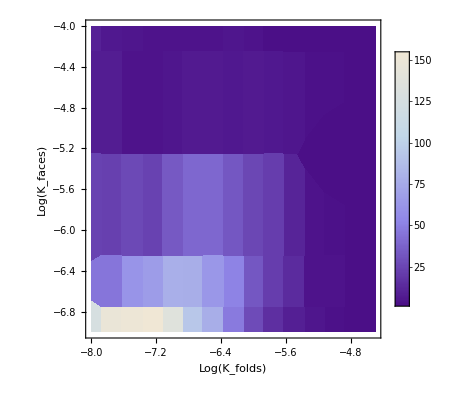

```mathematica
finalsmall=ListDensityPlot[Join[statedata4,statedata45,statedata5,statedata55,statedata6,statedata65,statedata7,statedatafold45,statedatafold425],PlotRange->{1,160},ColorFunction->"LakeColors",InterpolationOrder->0,PlotLegends->Automatic,FrameLabel->{"Log(K_folds)","Log(K_faces)"},ClippingStyle->Gray,LabelStyle->{FontSize->16}]
```

And combine the mask and plot for the final plot as it appears in the paper:

```mathematica
Show[finalsmall,masksmall]
```

ColorData::notent: {PigeonTones} is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

-Graphics-